## Type I Variant model

## 1. Possible Scenarios

```mathematica
Quit[]
```

#### FeynArts

```mathematica
(* Activate FeynArts *)
$LoadFeynArts=True;
$FeynCalcSartupMessages=False;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
(* Load FR model *)

modelfile="Type_I_variant";

InitializeModel[modelfile, GenericModel->modelfile]
```

True

```mathematica
(* Decay width *)
topo=CreateTopologies[0,1->2];
decaydiag[ii_]:=InsertFields[topo,{S[2]}->{F[ii],F[ii]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile]
```

```mathematica
RawdecAmp[ii_]:=
CreateFeynAmp[decaydiag[ii]]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}
FCdecamp[ii_]:=(FCFAConvert[RawdecAmp[ii],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1},OutgoingMomenta->{p2,p3}])//Contract//DiracSimplify

AmpSq[ii_]:=Simplify[DiracSimplify[FermionSpinSum[FCdecamp[ii]ComplexConjugate[FCdecamp[ii]]]]]
```

```mathematica
(4π)/(32 π^2 mphi)1/2 1/2 AmpSq[1]/.Pair[Momentum[p2],Momentum[p3]]->1/2 mphi^2+mnl1^2
```

(lphiN^2 mnl1^2 mphi)/(16 π mN1^2)

```mathematica
(4π)/(32 π^2 mphi)1/2 1/2 AmpSq[7]/.Pair[Momentum[p2],Momentum[p3]]->1/2 mphi^2+mchi^2
```

(lphichi^2 mphi)/(16 π)

### Cross section Calculation

#### Amplitudes n_l n_l → χ χ

```mathematica
topo=CreateTopologies[0,2->2];
diag[ii_,jj_]:=InsertFields[topo,{F[ii],F[jj]}->{F[7],F[7]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile]
```

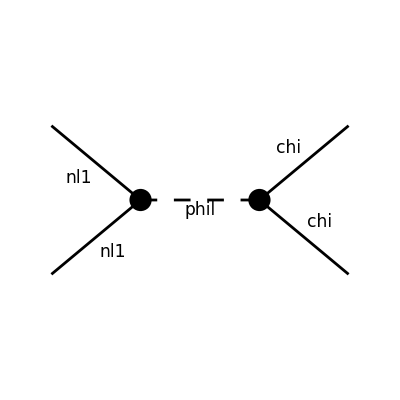

FeynArtsGraphics()(([]))

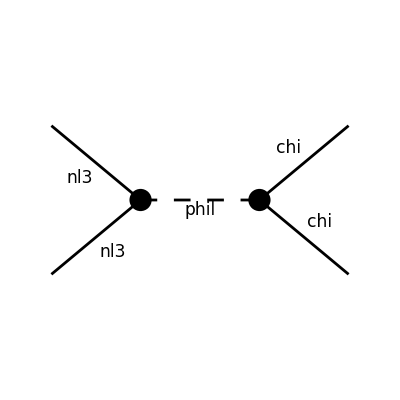

FeynArtsGraphics()(([]))

```mathematica
(* Diag 1 *)
diag1 = diag[1,1];
Paint[diag1,ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,150}]

(* Diag 2 *)
diag2 = diag[3,3];
Paint[diag2,ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,150}]
```

```mathematica
RawAmp[ii_,jj_]:=
CreateFeynAmp[diag[ii,jj]]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}
FCamp[ii_,jj_]:=(FCFAConvert[RawAmp[ii,jj],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4}])//Contract//DiracSimplify
FCamp2[ii_,jj_]:=FCamp[ii,jj]//.FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mphi]]:>1/(SP[p]-mphi^2+ⅈ mphi Γphi)

AmpSq[ii_,jj_,kk_,ll_]:=Simplify[DiracSimplify[FermionSpinSum[FCamp2[ii,jj]ComplexConjugate[FCamp2[kk,ll]]]]]
```

```mathematica
FCamp2[1,1]
```

-(lphichi lphiN mnl1 (φ(OverBar[p4],mchi)).(φ(-OverBar[p3],mchi)) (φ(-OverBar[p2],mnl1)).(φ(OverBar[p1],mnl1)))/(mN1 ((OverBar[p3]+OverBar[p4])^2-mphi^2+ⅈ Γphi mphi))

```mathematica
(4π)/(64 π^2 s)(*Phase Space*)1/4(*Spin Av.*)AmpSq[1,1,1,1]//.{Pair[Momentum[p1],Momentum[p2]]->1/2(s-2 mnl1^2),Pair[Momentum[p3],Momentum[p4]]->1/2(s-2 mchi^2),Pair[Momentum[p3+p4],Momentum[p3+p4]]->s}//Simplify
```

(lphichi^2 lphiN^2 mnl1^2 (4 mchi^2-s) (4 mnl1^2-s))/(16 π mN1^2 s (mphi^4+mphi^2 (Γphi^2-2 s)+s^2))